```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2796 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
(* 
Note on notation!!
q is for generalized coordinates , 
Q is for charge , 
e and E and for 2.718.....
*)

(* 
Also, distinction between s , ∂_t s , and r dot 
*)
```

```mathematica
Clear[s]
s = { r[t] Cos[θ[t]] , r[t] Sin[θ[t]] , z[t] }
```

{Cos[θ[t]] r[t],r[t] Sin[θ[t]],z[t]}

```mathematica
D[s, t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t],z'[t]}

```mathematica
D[s, t] . D[s, t]
```

z'[t]^2+(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 r'[t]^2+z'[t]^2+Cos[θ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
Simplify[Expand[ D[s, t] . D[s, t] ]] (* Notice order for when one goes to extract *) 
Simplify[Expand[ D[s, t] . D[s, t] ]]  // TraditionalForm
Sqrt[Simplify[Expand[ D[s, t] . D[s, t] ]] [[1]]] // PowerExpand
Sqrt[Simplify[Expand[ D[s, t] . D[s, t] ]] [[2]]] // PowerExpand
Sqrt[Simplify[Expand[ D[s, t] . D[s, t] ]] [[3]]] // PowerExpand
```

r'[t]^2+z'[t]^2+r[t]^2 θ'[t]^2

(r'(t))^2+(r(t))^2 (θ'(t))^2+(z'(t))^2

r'[t]

z'[t]

r[t] θ'[t]

```mathematica
Clear[rdot]
rdot = 
{ 
Sqrt[Simplify[Expand[ D[s, t] . D[s, t] ]] [[1]]] // PowerExpand , 
Sqrt[Simplify[Expand[ D[s, t] . D[s, t] ]] [[3]]] // PowerExpand , 
Sqrt[Simplify[Expand[ D[s, t] . D[s, t] ]] [[2]]] // PowerExpand
}
```

{r'[t],r[t] θ'[t],z'[t]}

```mathematica
Clear[T]
T = 1/2 m ( D[s, t] . D[s, t]  // Expand // Simplify )  ;
T // pdConv
```

1/2 m ((r(t))^2 ((∂θ(t))/(∂t))^2+((∂r(t))/(∂t))^2+((∂z(t))/(∂t))^2)

```mathematica
Clear[A]
A = { 0 , 1/2 B r[t] , 0 }
```

{0,1/2 B r[t],0}

```mathematica
Q rdot . A
```

1/2 B Q r[t]^2 θ'[t]

```mathematica
Clear[V]
V = - Q ϕ + Q rdot . A
```

-Q ϕ+1/2 B Q r[t]^2 θ'[t]

```mathematica
Clear[ℒ]
ℒ = T -  V  ;
ℒ // TraditionalForm
```

-1/2 B Q (r(t))^2 θ'(t)+1/2 m ((r'(t))^2+(r(t))^2 (θ'(t))^2+(z'(t))^2)+Q ϕ

```mathematica
Clear[q]
q = { r[t] , θ[t] , z[t] }
```

{r[t],θ[t],z[t]}

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

r[t] θ'[t] (-B Q+m θ'[t])-m r''[t]==0
r[t] (r'[t] (B Q-2 m θ'[t])-m r[t] θ''[t])==0
-m z''[t]==0

```mathematica
Clear[parameters]
parameters = { 
B-> 1 ,
Q-> 1 , 
m-> 1
};
parameters // TableForm
```

B→1
Q→1
m→1

```mathematica
eqs /. parameters  // TableForm
```

r[t] (-1+θ'[t]) θ'[t]-r''[t]==0
r[t] (r'[t] (1-2 θ'[t])-r[t] θ''[t])==0
-z''[t]==0

```mathematica
Clear[ics]
ics = { 
r[0] == 0.1 ,
r'[0] == 0.1 ,
θ[0] == 0.1 ,
θ'[0] == 0.1 ,
z[0] == 0.1 ,
z'[0] == 0.1 
};
ics // TableForm
```

r[0]==0.1
r'[0]==0.1
θ[0]==0.1
θ'[0]==0.1
z[0]==0.1
z'[0]==0.1

```mathematica
Clear[solution]
solution[t_] =
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 200 } ]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 10 } , PlotLabels-> q  ]
```

-Graphics-

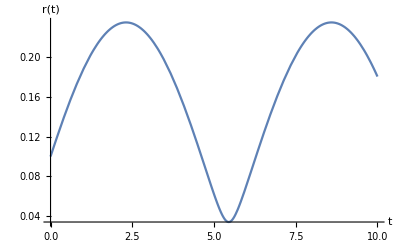

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t]]  , { t, 0, 10 }, AxesLabel->{ t,  q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```

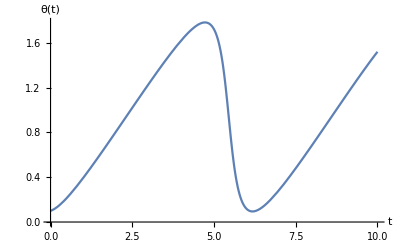

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t]]  , { t, 0, 10 }, AxesLabel->{ t,  q[[2]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } , PlotRange-> 4  ]  ,
{ tmax , 1 ,75 , 0.5  }  ]
```

```mathematica
Clear[𝓅]
𝓅 = Map[ p , q ]
```

{p[r[t]],p[θ[t]],p[z[t]]}

```mathematica
D[ ℒ , D[q[[1]], t] ] 
D[ ℒ , D[q[[2]], t] ] 
D[ ℒ , D[q[[3]], t] ]
```

m r'[t]

-1/2 B Q r[t]^2+m r[t]^2 θ'[t]

m z'[t]

```mathematica
Table[D[ ℒ , D[q[[i]], t] ]  == 𝓅[[i]] , { i, 1, 3 } ]  // TableForm
```

m r'[t]==p[r[t]]
-1/2 B Q r[t]^2+m r[t]^2 θ'[t]==p[θ[t]]
m z'[t]==p[z[t]]

```mathematica
Clear[momenta]
momenta = 
Flatten[Solve[Table[D[ ℒ , D[q[[i]], t] ]  == 𝓅[[i]] , { i, 1, 3 } ]  , D[q, t] ]]  ;
momenta // TableForm
```

r'[t]→p[r[t]]/m
θ'[t]→(2 p[θ[t]]+B Q r[t]^2)/(2 m r[t]^2)
z'[t]→p[z[t]]/m

```mathematica
Clear[ℋ]
ℋ = 
( Sum[ 𝓅[[i]] D[q[[i]], t] , { i, 1, 3 } ] - ℒ )   /. momenta // Expand
```

-Q ϕ+p[r[t]]^2/(2 m)+p[z[t]]^2/(2 m)+(B Q p[θ[t]])/(2 m)+p[θ[t]]^2/(2 m r[t]^2)+(B^2 Q^2 r[t]^2)/(8 m)